```mathematica
Solve[(1+z+1/2z^2)^2==1,z]
```

{{z→-2},{z→0},{z→-1-ⅈ √3},{z→-1+ⅈ √3}}

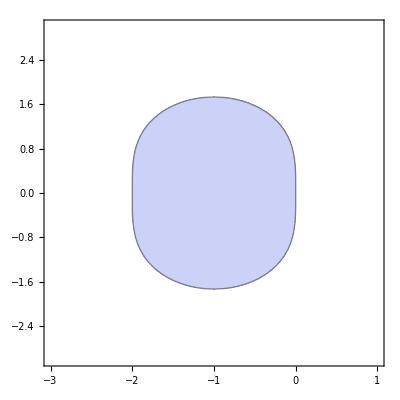

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x→-2-ⅈ y},{x→-ⅈ y}}

```mathematica
RegionPlot[Abs[1+x+I y+1/2(x+I y)^2]<1,{x,-3,1},{y,-3,3},Axes->True]
Solve[Abs[1+x+I y+1/2(x+I y)^2]==1,{x,y}]
```